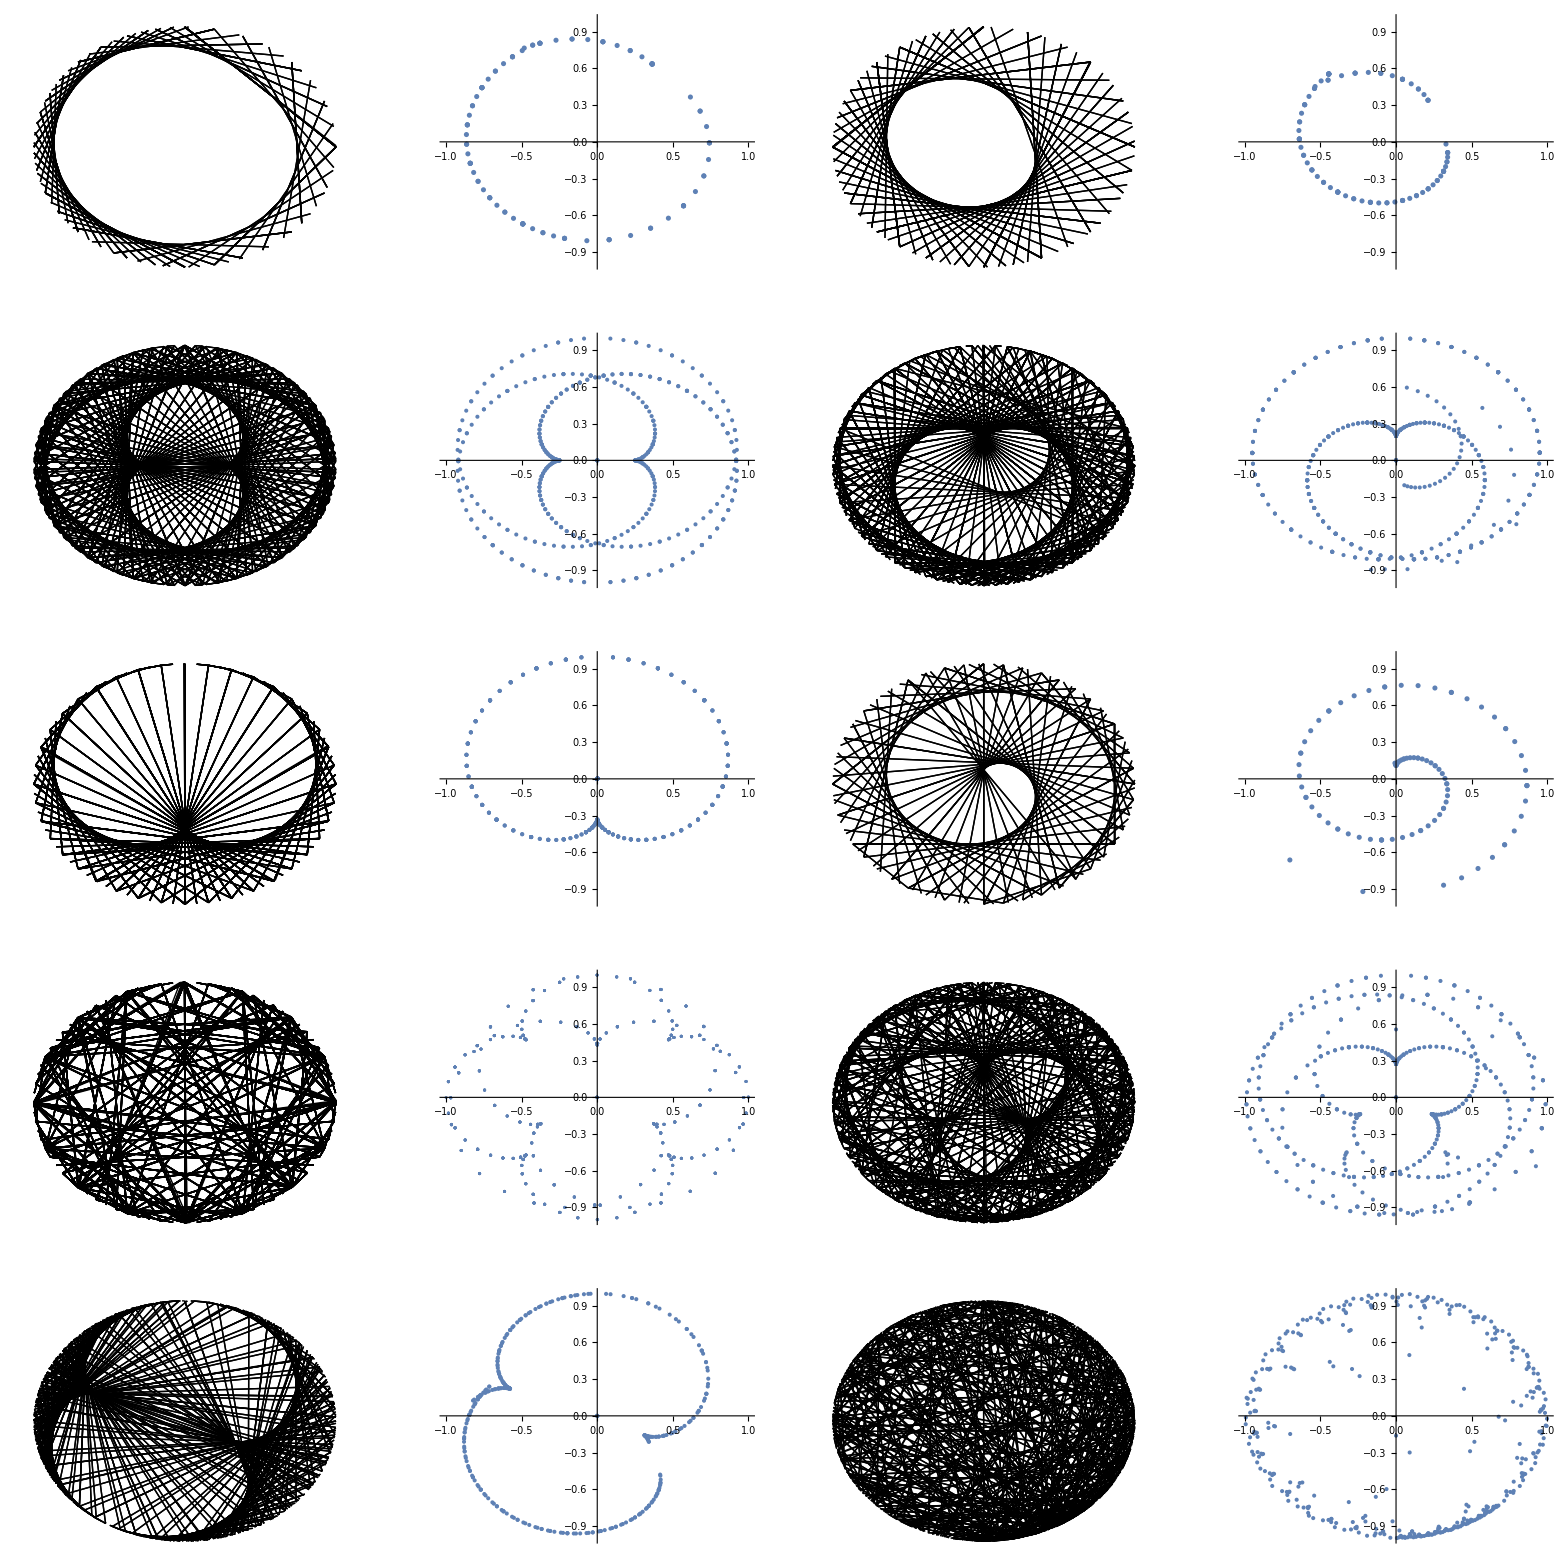

```mathematica
Remove[fnline,fnfact,rotate,intersect,intersectLines,start,stop,step,e];
rotate[n_]:=(alpha=2*Pi*fnfact[n];x=-Sin[alpha];y=Cos[alpha];{x,y});
(*intersect[n_,e_]:=(line1={rotate[n],rotate[fnline[n]]};line2={rotate[n+e],rotate[fnline[n+e]]};intersectLines[line1,line2,e]);*)

intersectLines[line1_,line2_]:=(
a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];If[det>0,{detx/det,dety/det},{0,0}]);

start=1;
stop=100;
step=1;
e=0.001;

fnline[n_]:=n*7;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p11=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p12=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
fnline[n_]:=n*10;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p13=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p14=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];

start=1;
stop=100;
step=0.2;
e=0.001;

fnline[n_]:=n*5;
fnfact[n_]:=n/(3^(Floor[Log[5,n]]+1)-3^Floor[Log[5,n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p21=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p22=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
fnline[n_]:=n*3;
fnfact[n_]:=n/(2^(Floor[Log[n]]+1)-2^Floor[Log[n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p23=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p24=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];

fnline[n_]:=n*4;
fnfact[n_]:=n/(2^(Floor[Log[n]]+1)-2^Floor[Log[n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p31=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p32=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
start=1;
stop=100;
step=1;
e=0.001;

fnline[n_]:=n*5;
fnfact[n_]:=n/(4^(Floor[Log[5,n]]+1)-4^Floor[Log[5,n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p33=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p34=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];

start=1;
stop=100;
step=0.1;
e=0.001;

fnline[n_]:=n*10;
fnfact[n_]:=n/(2^(Floor[Log[4,n]]+1)-2^Floor[Log[4,n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p41=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p42=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];

start=1;
stop=100;
step=0.2;
e=0.001;

fnline[n_]:=n*7;
fnfact[n_]:=n/(2^(Floor[Log[n]]+1)-2^Floor[Log[n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p43=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p44=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];

start=1;
stop=100;
step=0.3;
e=0.001;

fnline[n_]:=n^3;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p51=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p52=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];

start=1;
stop=100;
step=0.25;
e=0.001;

fnline[n_]:=2^n;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
p53=Graphics[Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
p54=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1];

GraphicsGrid[{{p11,p12,p13,p14},{p21,p22,p23,p24},{p31,p32,p33,p34},{p41,p42,p43,p44},{p51,p52,p53,p54}}]
```